```mathematica
k =2;
R= 3;
nu = 0.5;
beta = (1+nu)/2;
G[rx_,ry_,n_]= 1/(2*k^2)*(I/4*HankelH1[n,k*rx]*BesselJ[n,k*ry] - 1/(2*Pi)*BesselK[n,k*rx]*BesselI[n,k*ry]);
Gnxnxnxty[rx_,ry_,n_]= -(I*n)*D[G[rx,ry,n],{rx,3}];
Gnxtxtxty[rx_,ry_,n_] =  -(I*n)*Gnxtxtx[rx,ry,n];

Gnxnxnxny[rx_,ry_,n_]= D[G[rx,ry,n],{rx,3},{ry,1}];
Gnxnynyny[rx_,ry_,n_]= D[G[rx,ry,n],{rx,1},{ry,3}];
Gnxtxtx[rx_,ry_,n_]=-2/rx^3(I*n)^2 G[rx,ry,n]-1/rx^2 D[G[rx,ry,n],rx]+ (I*n)^2/rx^2 D[G[rx,ry,n],rx]+ 1/rx*D[G[rx,ry,n],{rx,2}];
Gnxtxtxny[rx_,ry_,n_] = D[Gnxtxtx[rx,ry,n],ry];
M4[rx_,ry_,n_] = Gnxnxnxny[rx,ry,n]+(2-nu)Gnytxtxtx[rx,ry,n];
```

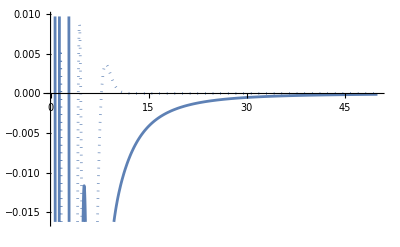

```mathematica
ReImPlot[Gnxnxnxny[R,R,n]*(2*Pi*R)-3/4Abs[n]/R- 1/(2*R),{n,0,50}]
```

```mathematica
ReImPlot[Gnxnynyny[R,R,n]*(2*Pi*R)-3/4Abs[n]/R+ 1/(2*R),{n,0,50}]
```

-Graphics-

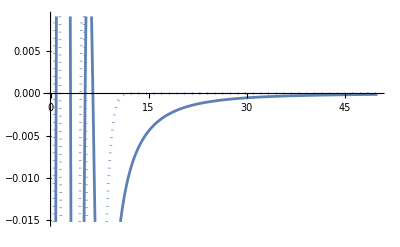

```mathematica
ReImPlot[Gnxtxtxny[R,R,n]*(2*Pi*R)+1/4Abs[n]/R+1/(2*R),{n,0,50}]
```

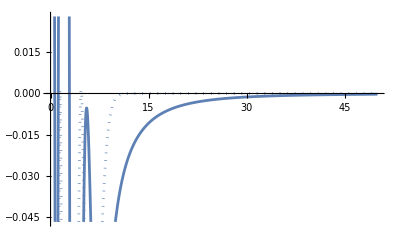

```mathematica
ReImPlot[M4[R,R,n]*(2*Pi*R)-beta/2*Abs[n]/R +(1-nu)/(2*R) ,{n,0,50}]
```

```mathematica
N[]
```

0.166667

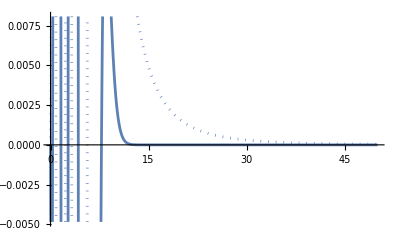

```mathematica
ReImPlot[Gnxnxnxty[R,R,n]*(2*Pi*R)+3I/2Abs[n]/R,{n,0,50}]
```

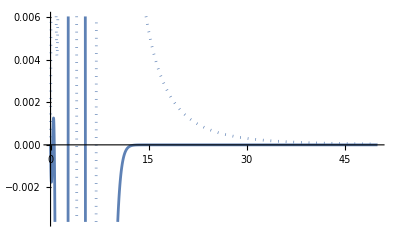

```mathematica
ReImPlot[Gnxtxtxty[R,R,n]*(2*Pi*R),{n,0,50}]
```